```mathematica
(* Survival of the fastest and the evolution of molecular complexity *)
(* Code for evolutionary dynamics *)
```

```mathematica
(* 1. Definitions *) 

(* binding threshold *) 
gamma1[l_, l0_] := gamma0 + l0/l

(* minimal length of functional sites, from condition gamma1[lmin,l0] + l0/(lmin gap) = 1 *) 
lmin[l0_] :=Ceiling[ l0 (gap+1)/((1 - gamma0)gap)] 

(* relative state entropy of binding site distribution and null distribution *) 
H[gamma_,l_,l0_]:= Log[Binomial[l,gamma l ] gamma0^(gamma l) (1 - gamma0)^((1-gamma) l)]
(* quadratic approximation *) 
H2[gamma_,l_,l0_]:= - l (gamma-gamma0)^2/(2 gamma0 (1 - gamma0)) 

(* fitness component of functional binding, depending on free energy gap *) 
pb[gamma_, l_,l0_]:= 1/(1+Exp[-gap (l/l0)(gamma - gamma1[l,l0])])
Fb[gamma_, l_,l0_,fb_]:= fb pb[gamma, l,l0]

(* Fitness component of genomic constraint *) 
Fc[gamma_, l_,l0_,fc_]:= - fc (l / l0 )

(* fitness component of spurious binding *) 
Fd[gamma_, l_,l0_,fd_]:= 0

(* total fitness *) 
F[gamma_, l_,l0_,fb_,fc_,fd_]:= Fb[gamma, l,l0,fb]+Fc[gamma, l,l0,fc]+Fd[gamma, l,l0,fd]

(* equilibrium free fitness, valid in all regimes *) 
Psi[gamma_, l_,l0_,fb_,fc_,fd_]:=F[gamma, l,l0,fb,fc,fd] + H[gamma,l,l0]

(* 1.1 Coding density dynamics *)

(* Kimura - Ohta substitution factors, depending on scaled selection coefficient *) 
g[s_]:= If[s^2 < 10^(-10), 1,s/(1- Exp[-s])]

(* substitution rates for binding changes *) 
(* (k,l) -> (k+1,l) *)
up[gamma_, l_, l0_,fb_,fc_,fd_,kappa_]:=
If[gamma<1, gamma0(1-gamma)(g[F[gamma+1/l, l, l0,fb,fc,fd]-F[gamma, l, l0,fb,fc,fd]]+ kappa ), 0]

(* (k,l) -> (k-1,l) *)
um[gamma_, l_, l0_,fb_,fc_,fd_,kappa_]:=
If[gamma>0,(1 - gamma0) gamma(g[F[gamma-1/l, l, l0,fb,fc,fd]-F[gamma, l, l0,fb,fc,fd]]+ kappa ),0]

(* evolutionary potential for trait dynamics *)
(* (i) full potential computed from full rate ratio up/um *)  
(* discrete values for k = 0, ..., l *)
Psiklist[l_,l0_,fb_,fc_,fd_,kappa_]:=
(gam0= (*Floor[gamma0 l]/l *)0;
dPsik= 0.;
plist = {{gam0,dPsik}};
Do[dPsik = dPsik + Log[up[gam-1/l, l, l0,fb,fc,fd,kappa]/um[gam, l, l0,fb,fc,fd,kappa]];
plist = Append[plist, {gam,dPsik}], 
{gam,gam0+1/l,1,1/l}])

(* interpolating function *) 
Psik[gamma_,l_,l0_,fb_,fc_,fd_,kappa_]:= 
(Psiklist[l,l0,fb,fc,fd,kappa];
Psikint = Interpolation[plist];
Psikint[gamma] - Psikint[gamma0])

(* (ii) fast-driving approximation *)  
PsikSClist[l_,l0_,fb_,fc_,fd_,kappa_]:=
(gam0= Floor[gamma0 l]/l ;
dPsik= 0.;
plist = {{gam0,dPsik}};
Do[dPsik = 
dPsik + Log[up[gam-1/l,l,l0,100 fb,fc,fd,kappa]/(100 (1-gamma0) gam kappa)];
plist = Append[plist, {gam,dPsik}], 
{gam,gam0+1/l,1,1/l}])

(* interpolating function *) 
PsikSC[gamma_,l_,l0_,fb_,fc_,fd_,kappa_]:= 
(PsikSClist[l,l0,fb,fc,fd,kappa];
PsikSCint = Interpolation[plist];
PsikSCint[gamma] -PsikSCint[gamma0])

(* (iii) slow-driving regime, non-equilibrium effective fitness and free fitness *) 
Fk[gamma_, l_,l0_,fb_,fc_,fd_,kappa_]:=(Fb[gamma, l,l0,fb]+Fd[gamma, l,l0,fd])/(1+kappa)+Fc[gamma, l,l0,fc]

PsikQ[gamma_, l_,l0_,fb_,fc_,fd_,kappa_]:=Fk[gamma, l,l0,fb,fc,fd,kappa] + H[gamma,l,l0]

(* speed of intrinsic trait evolution divided by point mutation rate *) 
gammadot[gamma_, l_,l0_,fb_,fc_,fd_]:=
up[gamma, l, l0,fb,fc,fd,kappa] - um[gamma, l, l0,fb,fc,fd,kappa]

(* ML value of coding density *) 
func = 1;
gammastar[l_,l0_,fb_,fc_,fd_,kappa_]:=
(Psiklist[l,l0,fb,fc,fd,kappa];
plist2 = Transpose[plist ][[2]];
gmax= 
If[func == 1, 
If[gamma1[l,l0] <1,
gmaxpos = Position[plist2, Max[Drop[plist2,Floor[l gamma1[l,l0]] ]]][[1,1]];
plist[[gmaxpos,1]],
1],
gmaxpos = Position[plist2, Max[plist2]][[1,1]];
 plist[[gmaxpos,1]]];
Psikint= Interpolation[plist];
gst= 
If[gmax==gam0, gamma0,
If[gmax ==1, 1,
plist3 =plist[[{gmaxpos-1,gmaxpos, gmaxpos+1}]];
Psifit= Fit[plist3, {1,x,x^2},x];
- Coefficient[Psifit,x,1]/(2Coefficient[Psifit,x,2])
]]) 

(* fitness, binding probability, and selection coefficient at stationary trait value for given l *) 
Fstar[l_,l0_,fb_,fc_,fd_,kappa_]:=F[gammastar[l,l0,fb,fc,fd,kappa],l,l0,fb,fc,fd]

pbstar[l_,l0_,fb_,fc_,fd_,kappa_]:=pb[gammastar[l,l0,fb,fc,fd,kappa],l,l0]


(* 1.2 Coding length dynamics *) 

(* length-changing mutation steps *)
(* (k,l) -> (k+1,l+1) *)
gammapp[gamma_,l_] := Min[(gamma + 1/l)/(1 + 1/l),1]
(* (k,l) -> (k,l+1) *)
gammapm[gamma_,l_] := Max[gamma /(1 + 1/l), gamma0]
(* (k,l) -> (k,l-1) *)
gammamp[gamma_,l_] := Min[gamma/(1 - 1/l), 1]
(* (k,l) -> (k-1,l-1) *)
gammamm[gamma_,l_] := Max[(gamma - 1/l)/(1 - 1/l), gamma0]

(* selection coeffcients for length increase and decrease *) 
spp[gamma_, l_,l0_,fb_,fc_,fd_]:= 
F[gammapp[gamma,l], l+1,l0,fb,fc,fd] - F[gamma, l,l0,fb,fc,fd] 

sppb[gamma_, l_,l0_,fb_]:= 
Fb[gammapp[gamma,l], l+1,l0,fb] - Fb[gamma, l,l0,fb] 

spm[gamma_, l_,l0_,fb_,fc_,fd_]:= 
F[gammapm[gamma,l], l+1,l0,fb,fc,fd] - F[gamma, l,l0,fb,fc,fd] 

smm[gamma_, l_,l0_,fb_,fc_,fd_]:= 
F[gammamm[gamma,l], l-1,l0,fb,fc,fd]-F[gamma, l,l0,fb,fc,fd] 

smp[gamma_, l_,l0_,fb_,fc_,fd_]:= 
F[gammamp[gamma,l], l-1,l0,fb,fc,fd] - F[gamma,l,l0,fb,fc,fd] 

smpb[gamma_, l_,l0_,fb_]:= 
Fb[gammamp[gamma,l], l-1,l0,fb] - Fb[gamma,l,l0,fb] 

(* substitution rates of length increase and decrease *) 
vpp[gamma_, l_,l0_,fb_,fc_,fd_]:= gamma0 g[spp[gamma, l,l0,fb,fc,fd]]

vpm[gamma_, l_,l0_,fb_,fc_,fd_]:= (1 - gamma0) g[spm[gamma, l,l0,fb,fc,fd]]

vplus[gamma_, l_,l0_,fb_,fc_,fd_]:= vpp[gamma, l,l0,fb,fc,fd] + vpm[gamma, l,l0,fb,fc,fd] 

vplusSC[gamma_, l_,l0_,fb_,fc_,fd_]:= gamma0 g[10 Max[spp[gamma, l,l0,fb,fc,fd],-1]]/10

vplusstar[l_,l0_,fb_,fc_,fd_,kappa_]:= vplus[gammastar[l,l0,fb,fc,fd,kappa],l,l0,fb,fc,fd]

vmm[gamma_, l_,l0_,fb_,fc_,fd_]:= gamma g[smm[gamma, l,l0,fb,fc,fd]] 

vmp[gamma_, l_,l0_,fb_,fc_,fd_]:= (1 - gamma) g[smp[gamma, l,l0,fb,fc,fd] ]

vminus[gamma_, l_,l0_,fb_,fc_,fd_]:= vmm[gamma, l,l0,fb,fc,fd] + vmp[gamma, l,l0,fb,fc,fd] 

vminusSC[gamma_, l_,l0_,fb_,fc_,fd_]:= (1 - gamma) g[10Max[smp[gamma, l,l0,fb,fc,fd],-1]]/10

vminusstar[l_,l0_,fb_,fc_,fd_,kappa_]:= vminus[gammastar[l,l0,fb,fc,fd,kappa],l,l0,fb,fc,fd]

(* ratchet selection coefficients *) 

ginv[u_] := s/. Solve[s/(1-Exp[-s])==u, s][[1]]

seffplus[l_,l0_,fb_,fc_,fd_,kappa_]:= ginv[N[vplusstar[l,l0,fb,fc,fd,kappa]]]

seffminus[l_,l0_,fb_,fc_,fd_,kappa_]:= ginv[N[vminusstar[l,l0,fb,fc,fd,kappa]]]

(* effective selection coefficient for length changes *) 

seff[l_,l0_,fb_,fc_,fd_,kappa_]:=  Log[vplusstar[ l-1,l0,fb,fc,fd,kappa]/vminusstar[ l,l0,fb,fc,fd,kappa]]

(* seff in SC approximation *) 
seffSC[l_,l0_,fb_,fc_,fd_,kappa_]:=  Log[(vplusSC[ gammastar[l-1,l0,fb,fc,fd,kappa],l-1,l0,fb,fc,fd]+0.001)/(vminusSC[gammastar[l,l0,fb,fc,fd,kappa],l,l0,fb,fc,fd]+0.001)]

(* ML value of code length *) 
lstar[l0_,fb_,fc_,fd_,kappa_]:= 
(gammastarlist = Table[If[ll<10, 1,gammastar[ll,ll0,ffb,ffc,0,kappa]],{ll,1,lmax}];
functposlist = {};
Do[If[gammastarlist[[ll]] > gamma1[ll, ll0]&& gammastarlist[[ll]]<1, functposlist = Append[functposlist, ll], Null], {ll,1,lmax}];
gammafunctlist = gammastarlist[[functposlist]];
lm= functposlist[[1]];
(* flist: discrete evolutionary potential for length, adds up seff *) 
flist = Table[
If[ll<= lm,Null,
Sum[ Log[vplus[ gammastarlist[[l1-1]],l1-1,l0,fb,fc,fd]/vminus[ gammastarlist[[l1]],l1,l0,fb,fc,fd]], {l1,lm+1, ll}]
],{ll,1,lmax}];
fmax= Max[Select[flist, #>0&]];
lst= Position[flist, fmax] [[1,1]];
(* flistSC: discrete evolutionary potential for length in SC approximation, adds up seffSC *) 
flistSC = Table[
If[ll<= lm,Null,
Sum[ Log[(vplusSC[ gammastarlist[[l1-1]],l1-1,l0,fb,fc,fd]+0.001)/(vminusSC[ gammastarlist[[l1]],l1,l0,fb,fc,fd]+0.001)]
, {l1,lm+1, ll}]],{ll,1,lmax}];
fmaxSC= Max[Select[flistSC, #>0&]];
lstSC= Position[flist, fmax] [[1,1]];
(* fpluslist: potential for extension *) 
seffpluslist = Table[
If[ll<= lm,Null,seffplus[ll,l0,fb,fc,fd, kappa]],{ll,1,lmax}];
fpluslist = Table[
If[ll<= lm,Null,
Sum[ seffpluslist[[l1]], {l1,lm+1, ll}]],{ll,1,lmax}];
(* fminuslist: potential for compression *) 
seffminuslist = Table[
If[ll<= lm,Null,seffminus[ll,l0,fb,fc,fd, kappa]],{ll,1,lmax}];
fminuslist = Table[
If[ll<= lm,Null,
-Sum[ seffminuslist[[l1]], {l1,lm+1, ll}]],{ll,1,lmax}])
```

```mathematica
(* 2. Simulation of evolutionary trajectories *) 

(* initialization at length l *) 
init[l_,l0_,fb_, fc_,fd_, kappa_]:= 
( Psiklist[l,l0,fb,fc,fd,kappa];
norm = Total[Exp[Transpose[plist][[2]]]];
pcumlist = Table[{plist[[k,1]], Sum[Exp[plist[[kk,2]]]/norm, {kk,1,k}]},{k,1,Length[plist]}];
r = Random[];
pt={Select[pcumlist, #[[2]]> r& ][[1,1]],l})

(* trait evolution step *) 

traitstep2[gl_, l0_,fb_,fc_,fd_,kappa_]:=
(pup = up[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa]/(up[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa]+um[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa]);
ppe= If[gl[[1]]<1, gamma0 (1-gl[[1]])kappa/up[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa],0];
pme= If[gl[[1]]> 0,(1-gamma0)gl[[1]] kappa/um[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa],0];
If[Random[]<pup,
pt = {gl[[1]]+1/gl[[2]], gl[[2]]}; 
If[Random[]<ppe, 
(*Print["external degradation" ]; *)
elist= Append[elist, pt];
next= next+1;
admutlist = Complement[admutlist, {pt}];
negmutlist = Complement[negmutlist, {pt}],

(* Print["adaptive mutation"];*)
elist= Complement[elist, {pt}];
admutlist = Append[admutlist, pt];
nad = nad +1;
negmutlist = Complement[negmutlist, {pt}]],

pt= {gl[[1]]-1/gl[[2]], gl[[2]]};
If[Random[]<pme, 
(* Print["external improvement" ];*) 
elist= Append[elist, pt];
next= next+1;
admutlist = Complement[admutlist, {pt}];
negmutlist = Complement[negmutlist, {pt}],

(* Print["deleterious mutation"];*)
elist= Complement[elist, {pt}];
admutlist = Complement[admutlist, {pt}];
negmutlist = Append[negmutlist, pt];
ndel = ndel +1;]
];
pt)

(* relative probability of length change *) 
rl[gl_, l0_,fb_,fc_,fd_,kappa_]:=
(vplus[gl[[1]],gl[[2]],l0,fb,fc,fd] +vminus[gl[[1]],gl[[2]],l0,fb,fc,fd])/(up[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa]+um[gl[[1]], gl[[2]], l0,fb,fc,fd,kappa])

(* length evolution step *) 
lengthstep2[gl_, l0_,fb_,fc_,fd_,kappa_]:=
(pup = vplus[gl[[1]],gl[[2]],l0,fb,fc,fd]/(vplus[gl[[1]],gl[[2]],l0,fb,fc,fd] +vminus[gl[[1]],gl[[2]],l0,fb,fc,fd]);
ppp = vpp[gl[[1]],gl[[2]],l0,fb,fc,fd]/vplus[gl[[1]],gl[[2]],l0,fb,fc,fd];
pmp =vmp[gl[[1]],gl[[2]],l0,fb,fc,fd]/vminus[gl[[1]],gl[[2]],l0,fb,fc,fd];
If[Random[]<pup,
(* extension *) 
If[Random[]<ppp,
pt={gammapp[gl[[1]],gl[[2]]], gl[[2]]+1};
adlist=Append[adlist, pt];
neglist=Complement[neglist,{pt}];
slist = Append[slist,spp[gl[[1]],gl[[2]],l0,fb,fc,fd]],
pt={gammapm[gl[[1]],gl[[2]]], gl[[2]]+1};
neglist=Append[neglist, pt];
adlist=Complement[adlist, {pt}];
slist = Append[slist,spm[gl[[1]],gl[[2]],l0,fb,fc,fd]]
],
(* compression *) 
If[Random[]<pmp,
pt={gammamp[gl[[1]],gl[[2]]], gl[[2]]-1};
adlist=Append[adlist, pt];
neglist=Complement[neglist,{pt}];
slist = Append[slist,smp[gl[[1]],gl[[2]],l0,fb,fc,fd]], 
pt={gammamm[gl[[1]],gl[[2]]], gl[[2]]-1};
neglist=Append[neglist, pt];
adlist=Complement[adlist, {pt}];
slist = Append[slist,smm[gl[[1]],gl[[2]],l0,fb,fc,fd]]
]];
pt)

(* evolutionary trajectories *)
evol2[lin_,l0_,fb_,fc_,fd_,kappa_,lambda_,t_]:=
(init[lin,l0,fb, fc,fd, kappa];
path={pt}; 
slist={};
elist={}; admutlist = {}; negmutlist = {};
adlist={}; neglist={};
lengthchanges=0; 
next = 0; nad=0;ndel= 0;
Do[
traitstep2[pt, l0,fb,fc,fd,kappa];
path=Append[path, pt];
r=N[rl[pt,l0,fb,fc,fd,kappa]];
If[Random[]< lambda r, 
lengthstep2[pt, l0,fb,fc,fd,kappa];
path=Append[path, pt];
lengthchanges =lengthchanges+1,
Null],
{tt,1,t}])

(* transformation to (k,l) coordinates *)
kltraj[path_]:= Table[{path[[t,2]],49-path[[t,1]]path[[t,2]]}, {t,1,Length[path]}]
```

```mathematica
(* 3. Evaluation of evolutionary potentials and ML values *) 

(* parameter values *) 
gamma0 = 1/4;
gap = 7;
ll0= 10;
lmax = 200;
ffb = 40 ll0;
ffc=  ll0; 
clist = ffc {1,0.7,0.5,0.35,0.2, 0.14,0.1};
kappalist = {0,0.2, 0.5,1,2,5,10,20,45};

(* potentials and ML values for coding density and length *)
(* starlist: output data: lm, lst, gammastarlist (l=1,...,lmax) *)starlistC = Table[lstar[ll0,ffb,clist[[j]],0,0]; {lm, lst, gammastarlist, flist, flistSC,fpluslist,fminuslist}, {j,1,Length[clist]}];
lmlistC = Transpose[starlistC][[1]];
lstarlistC = Transpose[starlistC][[2]];
gammastarlist2C= Transpose[starlistC][[3]];
flist2C= Transpose[starlistC][[4]];
flistSC2C= Transpose[starlistC][[5]];
fpluslist2C = Transpose[starlistC][[6]];
fminuslist2C = Transpose[starlistC][[7]];
gammalstarlistC =Table[gammastar[lstarlistC[[j]],ll0,ffb,clist[[j]],0,0], {j,1,Length[clist]}];

gammamlistC =Table[gammastar[lmlistC[[j]],ll0,ffb,clist[[j]],0,0], {j,1,Length[clist]}];
pbmlistC =Table[pb[gammamlistC[[j]],lmlistC[[j]],ll0], {j,1,Length[clist]}];
sstarlist2C = Table[F[gammastarlist2C[[j,l]]+1/l,l,ll0,ffb,clist[[j]],0]-F[gammastarlist2C[[j,l]],l,ll0,ffb,clist[[j]],0], {j,1,Length[clist]}, {l,1,lmax}];
PsiklognormlistC = Table[
Log[Sum[Exp[Psik[gamma,lstarlistC[[j]],ll0,ffb,0,0,0]]/lstarlistC[[j]],{gamma,0,1-1/lstarlistC[[j]], 1/lstarlistC[[j]]}]
], {j,1,Length[clist]}];
flognormlistC= Table[
Log[Sum[Exp[flist2C[[j,l]]],{l,lmlistC[[j]]+1,100}]
], {j,1,Length[clist]}];

starlist = Table[lstar[ll0,ffb,ffc,0,kappalist[[i]]]; {lm, lst, gammastarlist, flist, flistSC,fpluslist,fminuslist}, {i,1,Length[kappalist]}];
lmlist = Transpose[starlist][[1]];
lstarlist = Transpose[starlist][[2]];
gammastarlist2= Transpose[starlist][[3]];
flist2= Transpose[starlist][[4]];
flistSC2= Transpose[starlist][[5]];
fpluslist2 = Transpose[starlist][[6]];
fminuslist2 = Transpose[starlist][[7]];
gammalstarlist =Table[gammastar[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]], {i,1,Length[kappalist]}];
gammamlist =Table[gammastar[lmlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]], {i,1,Length[kappalist]}];
pbmlist =Table[pb[gammamlist[[i]],lmlist[[i]],ll0], {i,1,Length[kappalist]}];
sstarlist2 = Table[F[gammastarlist2[[i,l]]+1/l,l,ll0,ffb,ffc,0]-F[gammastarlist2[[i,l]],l,ll0,ffb,ffc,0], {i,1,Length[kappalist]}, {l,1,lmax}];
Psiklognormlist = Table[
Log[Sum[Exp[Psik[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]]/lstarlist[[i]],{gamma,0,1-1/lstarlist[[i]], 1/lstarlist[[i]]}]
], {i,1,Length[kappalist]}];
flognormlist= Table[
Log[Sum[Exp[flist2[[i,l]]],{l,lmlist[[i]]+1,100}]
], {i,1,Length[kappalist]}];

Print["coding density and code length depending on complexity cost c at κ = 0:"]
Print[MatrixForm[{
Prepend[clist/ffc, "c"],
Prepend[lstarlistC, "l^*(c)"],
Prepend[Round[gammalstarlistC, 0.01], "γ^*(c)"]}]]

Print["coding density and code length depending on driving rate κ at c = 0:"]
Print[MatrixForm[{
Prepend[kappalist, "κ"],
Prepend[lstarlist, "l^*(κ)"],
Prepend[Round[gammalstarlist, 0.01], "γ^*(κ)"]}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

coding density and code length depending on complexity cost c at κ = 0:

(c | 1 | 0.7 | 0.5 | 0.35 | 0.2 | 0.14 | 0.1
l^*(c) | 27 | 31 | 36 | 43 | 59 | 72 | 89
γ^*(c) | 0.86 | 0.79 | 0.73 | 0.65 | 0.55 | 0.5 | 0.45)

coding density and code length depending on driving rate κ at c = 0:

(κ | 0 | 0.2 | 0.5 | 1 | 2 | 5 | 10 | 20 | 45
l^*(κ) | 27 | 29 | 32 | 35 | 38 | 46 | 54 | 64 | 79
γ^*(κ) | 0.86 | 0.81 | 0.75 | 0.69 | 0.64 | 0.56 | 0.5 | 0.45 | 0.4)

```mathematica
(* 4. Code for figures *)
```

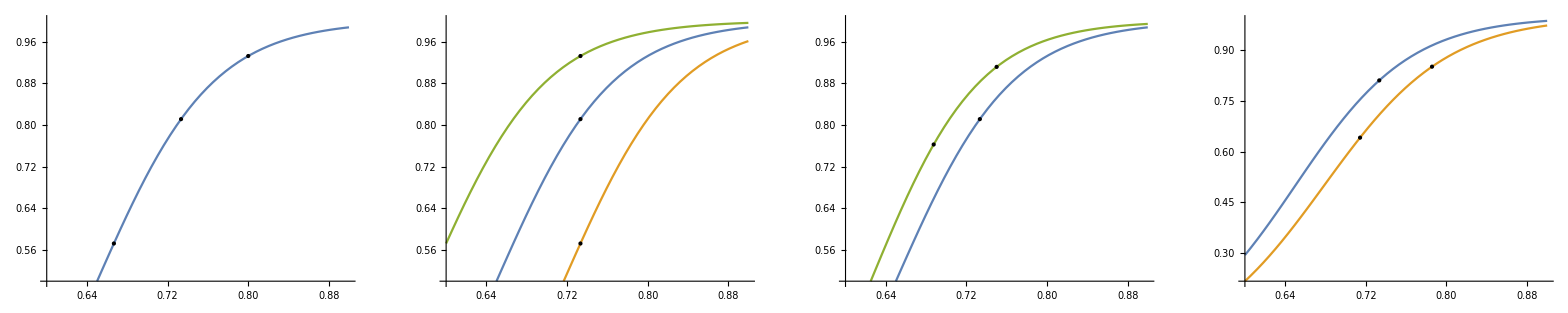

```mathematica
(* Figure 1: Evolutionary steps for coding density  *)
GraphicsGrid[{{
(* recognition site mutations *) 
Show[Plot[Fb[gamma, 15,6,1],{gamma,0.6,0.9}, 
PlotRange ->{0.5,1}], 
Graphics[{Point[{11/15, Fb[11/15, 15,6,1]}]}],
Graphics[{Point[{12/15, Fb[12/15, 15,6,1]}]}],
Graphics[{Point[{10/15, Fb[10/15, 15,6,1]}]}]],
(* recognition target mutations *) 
Show[Plot[{Fb[gamma, 15,6,1], Fb[gamma-1/15,15,6,1], Fb[gamma+1/15,15,6,1]},{gamma,0.6,0.9}, PlotRange ->{0.5,1}],
Graphics[{Point[{11/15, Fb[11/15, 15,6,1]}]}],
Graphics[{Point[{11/15, Fb[10/15, 15,6,1]}]}],
Graphics[{Point[{11/15, Fb[12/15, 15,6,1]}]}]],
(* recognition site extensions *) 
Show[Plot[{Fb[gamma, 15,6,1],  Fb[gamma,16,6,1]},{gamma,0.6,0.9}, 
PlotRange ->{0.5,1},PlotStyle->{ColorData[97,1], ColorData[97,3]}],
Graphics[{Point[{11/15, Fb[11/15, 15,6,1]}]}],
Graphics[{Point[{12/16, Fb[12/16, 16,6,1]}]}],
Graphics[{Point[{11/16, Fb[11/16, 16,6,1]}]}]],
(* recognition site compressions *)
Show[Plot[{Fb[gamma, 15,6,1], Fb[gamma,14,6,1]},{gamma,0.6,0.9}],
Graphics[{Point[{11/15, Fb[11/15, 15,6,1]}]}],
Graphics[{Point[{11/14, Fb[11/14, 14,6,1]}]}],
Graphics[{Point[{10/14, Fb[10/14, 14,6,1]}]}]
]}}]
```

```mathematica
(* Figure 2: Statistics and evolutionary trajectories of recognition sites *)

(* matrices of joint distribution Psi(k,l), all sites and functional sites *) 
 mm[ii_,lmax_,kmax_]:= 
(pot = Table[ 
Psiklist[l,ll0,ffb,0,0,kappalist[[ii]]]; 
pl = Transpose[plist][[2]] ;
pl= If[l<kmax,Join[pl, Table[0,{k,1,kmax-l}]],
Take[pl,kmax+1]];
pl = pl - Max[pl];
pl +flist2[[ii,l]]-flist2[[ii,lstarlist[[ii]] ]] /. Null ->-50,
{l,1,lmax}];
pot = Transpose[pot];
Table[Max[Exp[pot[[k,l]]]-0.05,0],{k,1,kmax},{l,1,lmax}])

mmfunc[ii_,lmax_,kmax_]:= 
(pot = Table[ 
Psiklist[l,ll0,ffb,0,0,kappalist[[ii]]]; 
pl = Transpose[plist][[2]] ;
pl= If[l<kmax,Join[pl, Table[0,{k,1,kmax-l}]],
Take[pl,kmax+1]];
pl = pl - Max[pl];
pl= pl +flist2[[ii,l]]-flist2[[ii,lstarlist[[ii]] ]] /. Null ->-50;
pl=Exp[pl] Table[pb[k/l,l,ll0],{k,0,kmax}],
{l,1,lmax}];
pot = Transpose[pot];
pot=pot/Max[pot];
Table[Max[ pot[[k,l]]-0.05,0],{k,1,kmax},{l,1,lmax}])

mmC[jj_,lmax_,kmax_]:= 
(pot = Table[ 
Psiklist[l,ll0,ffb,clist[[jj]],0,0]; 
pl = Transpose[plist][[2]] ;
pl= If[l<kmax,Join[pl, Table[0,{k,1,kmax-l}]],
Take[pl,kmax+1]];
pl = pl - Max[pl];
pl +flist2[[jj,l]]-flist2[[kk,lstarlistC[[jj]] ]] /. Null ->-50,
{l,1,lmax}];
pot = Transpose[pot];
Table[Max[Exp[pot[[k,l]]]-0.05,0],{k,1,kmax},{l,1,lmax}])

mmfuncC[jj_,lmax_,kmax_]:= 
(pot = Table[ 
Psiklist[l,ll0,ffb,clist[[jj]],0,0]; 
pl = Transpose[plist][[2]] ;
pl= If[l<kmax,Join[pl, Table[0,{k,1,kmax-l}]],
Take[pl,kmax+1]];
pl = pl - Max[pl];
pl= pl +flist2C[[jj,l]]-flist2C[[jj,lstarlistC[[jj]] ]] /. Null ->-50;
pl=Exp[pl] Table[pb[k/l,l,ll0],{k,0,kmax}],
{l,1,lmax}];
pot = Transpose[pot];
pot=pot/Max[pot];
Table[Max[ pot[[k,l]]-0.05,0],{k,1,kmax},{l,1,lmax}])

(* run 1 for Fig. 2 *) 
evol2[20,ll0,ffb,ffc,0,0,0.1,1000];
Print[next]
Print[ nad]
Print[ ndel]

path0 = path; 
admutlist0= admutlist;
negmutlist0 = negmutlist;
elist0 = elist;
adlist0=adlist;
neglist0= neglist;
```

0

494

506

```mathematica
(* run 2 for Fig. 2 *) 
evol2[89,ll0,ffb,0.1 ffc,0,0,0.1,3000];
Print[next]
Print[ nad]
Print[ ndel]

path01 = path; 
admutlist01 = admutlist;
negmutlist01 = negmutlist;
elist01 = elist;
adlist01=adlist;
neglist01= neglist;
```

0

1489

1511

```mathematica
(* run 3 for Fig. 2 *) 
evol2[79,ll0,2 ffb,ffc,0,45,0.1,4000];
Print[next]
Print[ nad]
Print[ ndel]

path45 = path; 
admutlist45 = admutlist;
negmutlist45 = negmutlist;
elist45 = elist;
adlist45=adlist;
neglist45= neglist;
```

3093

905

2

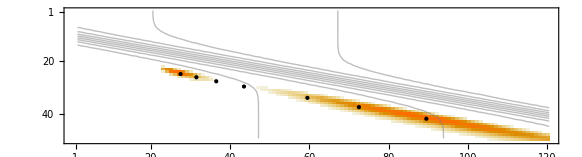

-Graphics-

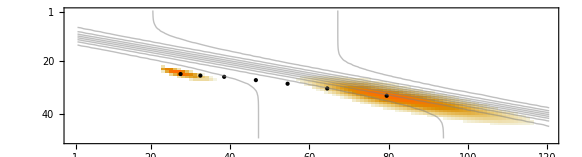

-Graphics-

```mathematica
(* plot Figure 2 *)  
fig2a= 
Show[
MatrixPlot[1- (1- mmfunc[1,120,50])(1-mmfuncC[7,120,50]),AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30,40,50},{1,10,20,30,40,50}},{{1,20,40,60,80,100,120}, None}}], 
Graphics[Table[{PointSize[Medium],Black,Point[{lstarlistC[[j]], 49-lstarlistC[[j]] gammalstarlistC[[j]]}]}, {j,{1,2,3,4,5,6,7}}]],

(* Contours *) 
(*ContourPlot[0.75 + 0.3 F[(45-k)/l,l,ll0,ffb,ffc,0] /ffb, {l,1,120} ,{k,1,45},Contours->10, ContourShading -> True, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray]*)
ContourPlot[0.75 + 0.3F[(50-k)/l,l,ll0,ffb,ffc,0]/ffb , {l,1,120} ,{k,1,50},Contours->10, 
ContourShading -> False, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray]

(* FrameLabel->{"code length, StyleBox[\"l\",FontSlant->\"Italic\"]","number of matches, StyleBox[\"k\",FontSlant->\"Italic\"]"}*)]

fig2b= Show[
MatrixPlot[Table[0, {k,1,50}, {l,1,120}],AspectRatio->0.27,
FrameTicks->{{{1,10,20,30,40,50},{1,10,20,30,40,50}},{{1,20,40,60,80,100,120}, None(* {1,20,40,60,80,100,120}*)}}], 
(* Contours *) 
ContourPlot[0.75 + 0.3 F[(50-k)/l,l,ll0,ffb,ffc,0] /ffb, {l,1,120} ,{k,1,50},Contours->10, ContourShading -> True, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray],

(* path at c = 1, kappa = 0 *) 
Graphics[{ColorData[97,1],Line[kltraj[path0]]}],
Graphics[{ColorData[97,3],PointSize[0.005],
Table[Point[{admutlist0[[i,2]], 49 - admutlist0[[i,1]]admutlist0[[i,2]]}],{i,1,Length[admutlist0]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.005],
Table[Point[{negmutlist0[[i,2]], 49 - negmutlist0[[i,1]]negmutlist0[[i,2]]}],{i,1,Length[negmutlist0]}]}],
Graphics[{ColorData[97,4],PointSize[0.005],
Table[Point[{elist0[[i,2]], 49 - elist0[[i,1]]elist0[[i,2]]}],{i,1,Length[elist0]}]}],

(* path at c = 0.1, kappa = 0 *) 
Graphics[{ColorData[97,1],Line[kltraj[path01]]}],
Graphics[{ColorData[97,3],PointSize[0.005],
Table[Point[{admutlist01[[i,2]], 49 - admutlist01[[i,1]]admutlist01[[i,2]]}],{i,1,Length[admutlist01]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.005],
Table[Point[{negmutlist01[[i,2]], 49 - negmutlist01[[i,1]]negmutlist01[[i,2]]}],{i,1,Length[negmutlist01]}]}],
Graphics[{ColorData[97,4],PointSize[0.005],
Table[Point[{elist01[[i,2]], 49 - elist01[[i,1]]elist01[[i,2]]}],{i,1,Length[elist01]}]}]

(* FrameLabel->{"code length, StyleBox[\"l\",FontSlant->\"Italic\"]","number of matches, StyleBox[\"k\",FontSlant->\"Italic\"]"}*) ]

fig2c= 
Show[
MatrixPlot[1- (1- mmfunc[1,120,50])(1-mmfunc[9,120,50]),AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30,40,50},{1,10,20,30,40,50}},{{1,20,40,60,80,100,120}, None}}], 
Graphics[Table[{PointSize[Medium],Black,Point[{lstarlist[[i]], 49-lstarlist[[i]] gammalstarlist[[i]]}]}, {i,{1,3,5,6,7,8,9}}]],

(* Contours *) 
(*ContourPlot[0.75 + 0.3 F[(45-k)/l,l,ll0,ffb,ffc,0] /ffb, {l,1,120} ,{k,1,45},Contours->10, ContourShading -> True, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray]*)
ContourPlot[0.75 + 0.3F[(50-k)/l,l,ll0,ffb,ffc,0]/ffb , {l,1,120} ,{k,1,50},Contours->10, 
ContourShading -> False, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray]

(* FrameLabel->{"code length, StyleBox[\"l\",FontSlant->\"Italic\"]","number of matches, StyleBox[\"k\",FontSlant->\"Italic\"]"}*) ]

fig2d= Show[
MatrixPlot[Table[0, {k,1,50}, {l,1,120}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30,40,50},{1,10,20,30,40,50}},{{1,20,40,60,80,100,120}, None}}], 
(* Contours *) 
(* ContourPlot[0.75 + 0.3 F[(45-k)/l,l,ll0,ffb,ffc,0] /ffb, {l,1,120} ,{k,1,45},Contours->10, ContourShading -> True, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray], *)
ContourPlot[0.75 + 0.3 F[(50-k)/l,l,ll0,ffb,ffc,0] /ffb, {l,1,120} ,{k,1,50},Contours->10, ContourShading -> True, ColorFunction -> GrayLevel, ColorFunctionScaling -> False, ContourStyle-> Gray],

(* path at c = 1, kappa = 0 *) 
Graphics[{ColorData[97,1],Line[kltraj[path0]]}],
Graphics[{ColorData[97,3],PointSize[0.005],
Table[Point[{admutlist0[[i,2]], 49 - admutlist0[[i,1]]admutlist0[[i,2]]}],{i,1,Length[admutlist0]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.005],
Table[Point[{negmutlist0[[i,2]], 49 - negmutlist0[[i,1]]negmutlist0[[i,2]]}],{i,1,Length[negmutlist0]}]}],
Graphics[{ColorData[97,4],PointSize[0.005],
Table[Point[{elist0[[i,2]], 49 - elist0[[i,1]]elist0[[i,2]]}],{i,1,Length[elist0]}]}],

(* path at c = 1, kappa = 45 *) 
Graphics[{ColorData[97,1],Line[kltraj[path45]]}],
Graphics[{ColorData[97,3],PointSize[0.005],
Table[Point[{admutlist45[[i,2]], 49 - admutlist45[[i,1]]admutlist45[[i,2]]}],{i,1,Length[admutlist45]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.005],
Table[Point[{negmutlist45[[i,2]], 49 - negmutlist45[[i,1]]negmutlist45[[i,2]]}],{i,1,Length[negmutlist45]}]}],
Graphics[{ColorData[97,4],PointSize[0.005],
Table[Point[{elist45[[i,2]], 49 - elist45[[i,1]]elist45[[i,2]]}],{i,1,Length[elist45]}]}]

(* FrameLabel->{"code length, StyleBox[\"l\",FontSlant->\"Italic\"]","number of matches, StyleBox[\"k\",FontSlant->\"Italic\"]"}, LabelStyle -> FontSize->14 *) ]
```

```mathematica
(* Figure 3: Ratchet evolution of coding length *)
```

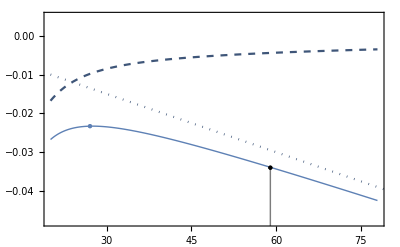

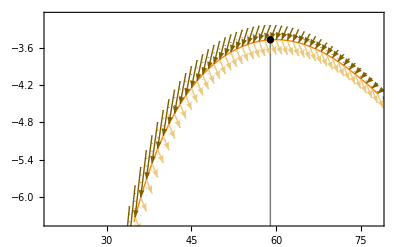

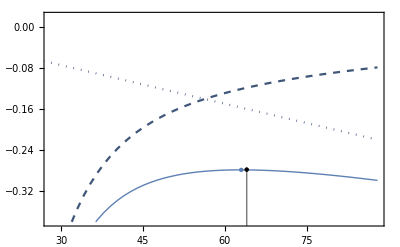

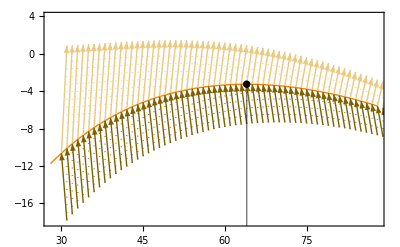

```mathematica
p3a = Show[
Table[ft=Fit[Table[{l,F[gammastarlist2C[[j,l]],l,ll0,ffb,clist[[j]],0]/ffb -1}, {l,lmlistC[[j]]+1,100}],{1/l,1/l^2,1/l^3,l},l];
Plot[ft,{l,20,78},
PlotRange ->{-0.048,0.005},ImageSize-> 400, AspectRatio -> 1/GoldenRatio, 
Frame -> True, 
(* FrameTicks->{{{-0.04,-0.02,0},None},{None,None}},*) 
(*FrameLabel->{"code length, l","fitness, F̄"},*)
PlotStyle -> {Thick, ColorData[97,1]}],
{j,{5}}],

Table[ft=Fit[Table[{l,(pb[gammastarlist2C[[j,l]],l,ll0]-1)}, {l,lmlistC[[j]]+1,100}],
{1/l,1/l^2,1/l^3,l},l];
Plot[ft, {l,20,78},
Frame -> True, PlotStyle -> {Dashed, Darker[ColorData[97,1]]}, PlotRange ->{-100,0}],{j,{5}}],
ListPlot[Table[{lstarlistC[[j]],(pb[gammalstarlist[C[j]],lstarlistC[[j]],ll0]-1)}, {j,{5}}],
PlotStyle-> {Black, PointSize[Medium]}, Filling-> -100],

Plot[-clist[[5]] l/(ll0 ffb), {l,20,88}, PlotStyle -> {Dotted,Darker[ColorData[97,1]]}], 

Table[ft=Fit[Table[{l,F[gammastarlist2C[[j,l]],l,ll0,ffb,clist[[j]],0]/ffb -1}, {l,lmlistC[[j]]+1,100}],{1/l,1/l^2,1/l^3,l},l];
ft1= Table[ft /. l->ll,{ll,15,100}];
lmax= Position[ft1, Max[ft1]][[1,1]] +14;
ListPlot[{{lmax, ft/. l-> lmax}},
PlotStyle-> {ColorData[97,1], PointSize[Medium]}
(* Filling ->-100, FillingStyle -> { Thin, Dotted} *)],
{j,{5}}],
ListPlot[Table[{lstarlistC[[j]],F[gammastarlist2C[[j,lstarlistC[[j]]]],lstarlistC[[j]],ll0,ffb,clist[[j]],0] /ffb-1},{j,{5}}],
PlotStyle-> {Black, PointSize[Medium]},
Filling ->-100 ],
ImageSize->{400,400}
]

p3b = Show[
Table[ft=Fit[
Table[{l,flist2C[[j,l]]-flognormlistC[[j]]}, {l,lmlistC[[j]]+1,100}],{1,l,l^2,l^3, l^4, l^5, l^6},l];
Plot[ft,{l,20,78}, PlotRange->{-6.4,-3.1},ImageSize-> 420, 
PlotStyle -> {Thick,Orange}, AspectRatio -> 1/GoldenRatio, 
Frame -> True
(*FrameLabel->{"code length, l", "potential, Ψ,  ratchet selection, s_±"}*)],{j,{5}}],
Table[
ft=Fit[Table[{l,fpluslist2C[[j,l]]}, {l,lmlistC[[j]]+1,100}],
{1,l,l^2,l^3, l^4, l^5, l^6},l];
ft2=Fit[Table[{l,flist2C[[j,l]]-flognormlistC[[j]]}, {l,lmlistC[[j]]+1,100}],{1,l,l^2,l^3, l^4, l^5, l^6},l];
Table[offset = (ft2 /. l-> lstart)-(ft /. l-> lstart);
pt1={lstart, (ft /. l-> lstart) + offset};
pt2= {lstart+1, (ft /. l-> (lstart+1)) + offset};
pt3= {lstart+1, (ft2 /. l-> (lstart+1))};
Graphics[
{{RGBColor[235/255,201/255,127/255],Arrowheads[0.02],Arrow[{pt1,pt2}]},
{Dotted, RGBColor[235/255,201/255,127/255],Line[{pt2,pt3}]}}],
{lstart, lmlistC[[j]]+1,89}],
{j,{5}}],
Table[
ft=Fit[Table[{l,fminuslist2C[[j,l]]}, {l,lmlistC[[j]]+1,100}],
{1,l,l^2,l^3, l^4, l^5, l^6},l];
ft2=Fit[Table[{l,flist2C[[j,l]]-flognormlistC[[j]]}, {l,lmlistC[[j]]+1,100}],{1,l,l^2,l^3, l^4, l^5, l^6},l];
Table[offset = (ft2 /. l-> lstart)-(ft /. l-> lstart);
pt1={lstart, (ft /. l-> lstart) + offset};
pt2= {lstart+1, (ft /. l-> (lstart+1)) + offset};
pt3= {lstart+1, (ft2 /. l-> (lstart+1))};
Graphics[
{{RGBColor[127/255,96/255,0/255],Arrowheads[0.02],Arrow[{pt2,pt1}]},
{Dotted, RGBColor[127/255,96/255,0/255],Line[{pt2,pt3}]}}],
{lstart, lmlistC[[j]]+1,89}],
{j,{5}}],
ListPlot[Table[{lstarlistC[[j]],flist2C[[j,lstarlistC[[j]]]]-flognormlistC[[j]]}, {j,{5}}], PlotStyle -> Black, Filling -> -10]
(*ListPlot[Table[{lstarlistC[[j]],flist2C[[j,lstarlistC[[j]]]]-flognormlistC[[j]]}, {j,{5}}], PlotStyle -> Black, Filling -> 1]*),
ImageSize->{400,400}
]

p3c = Show[
Table[ft=Fit[Table[{l,F[gammastarlist2[[i,l]],l,ll0,ffb,ffc,0]/ffb -1}, {l,lmlist[[i]]+1,100}],{1/l,1/l^2,1/l^3,l},l];
Plot[ft,{l,28,88},
PlotRange ->{-0.38,0.02},ImageSize-> 400, AspectRatio -> 1/GoldenRatio, 
Frame -> True, 
(* FrameTicks->{{{-0.3,-0.2,-0.1,0},None},{None,None}},*) 
(*FrameLabel->{"code length, l","fitness, F̄"},*)
PlotStyle -> {Thick, ColorData[97,1]}],
{i,{8}}],

Table[ft=Fit[Table[{l,(pb[gammastarlist2[[i,l]],l,ll0]-1)}, {l,lmlist[[i]]+1,100}],
{1/l,1/l^2,1/l^3,l},l];
Plot[ft, {l,28,88},
Frame -> True, PlotStyle -> {Dashed, Darker[ColorData[97,1]]}, PlotRange ->{-100,0}],{i,{8}}],
(*ListPlot[Table[{lstarlist[[i]],(pb[gammalstarlist[[i]],lstarlist[[i]],ll0]-1)}, {i,{8}}],
PlotStyle-> {Black, PointSize[Medium]}, Filling-> -100], *)

Plot[-ffc l/(ll0 ffb), {l,15,88}, PlotStyle -> {Dotted,Darker[ColorData[97,1]]}], 

Table[ft=Fit[Table[{l,F[gammastarlist2[[i,l]],l,ll0,ffb,ffc,0]/ffb -1}, {l,lmlist[[i]]+1,100}],{1/l,1/l^2,1/l^3,l},l];
ft1= Table[ft /. l->ll,{ll,15,100}];
lmax= Position[ft1, Max[ft1]][[1,1]] +14;
ListPlot[{{lmax, ft/. l-> lmax}},
PlotStyle-> {ColorData[97,1], PointSize[Medium]}
(* Filling ->-100, FillingStyle -> { Thin, Dotted} *)],
{i,{8}}],
ListPlot[Table[{lstarlist[[i]],F[gammastarlist2[[i,lstarlist[[i]]]],lstarlist[[i]],ll0,ffb,ffc,0] /ffb-1},{i,{8}}],
PlotStyle-> {Black, PointSize[Medium]},Filling ->-100 ],
ImageSize->{400,400}
]

p3d = Show[
Table[ft=Fit[
Table[{l,flist2[[i,l]]-flognormlist[[i]]}, {l,lmlist[[i]]+1,100}],{1,l,l^2,l^3, l^4, l^5, l^6},l];
Plot[ft,{l,28,88}, PlotRange->{-18,4},ImageSize-> 420, 
PlotStyle -> {Thick,Orange}, AspectRatio -> 1/GoldenRatio, 
Frame -> True, Axes-> False
(* FrameLabel->{"code length, l", "potential, Ψ,  ratchet selection, s_±"}*)],{i,{8}}],
Table[
ft=Fit[Table[{l,fpluslist2[[i,l]]}, {l,lmlist[[i]]+1,100}],
{1,l,l^2,l^3, l^4, l^5, l^6},l];
ft2=Fit[Table[{l,flist2[[i,l]]-flognormlist[[i]]}, {l,lmlist[[i]]+1,100}],{1,l,l^2,l^3, l^4, l^5, l^6},l];
Table[offset = (ft2 /. l-> lstart)-(ft /. l-> lstart);
pt1={lstart, (ft /. l-> lstart) + offset};
pt2= {lstart+1, (ft /. l-> (lstart+1)) + offset};
pt3= {lstart+1, (ft2 /. l-> (lstart+1))};
Graphics[
{{(*ColorData[97,3]*) RGBColor[235/255,201/255,127/255],Arrowheads[0.02],Arrow[{pt1,pt2}]},
{(*ColorData[97,3]*) Dotted, RGBColor[235/255,201/255,127/255],Line[{pt2,pt3}]}}],
{lstart, lmlist[[i]]+1,89}],
{i,{8}}],
Table[
ft=Fit[Table[{l,fminuslist2[[i,l]]}, {l,lmlist[[i]]+1,100}],
{1,l,l^2,l^3, l^4, l^5, l^6},l];
ft2=Fit[Table[{l,flist2[[i,l]]-flognormlist[[i]]}, {l,lmlist[[i]]+1,100}],{1,l,l^2,l^3, l^4, l^5, l^6},l];
Table[offset = (ft2 /. l-> lstart)-(ft /. l-> lstart);
pt1={lstart, (ft /. l-> lstart) + offset};
pt2= {lstart+1, (ft /. l-> (lstart+1)) + offset};
pt3= {lstart+1, (ft2 /. l-> (lstart+1))};
Graphics[
{{RGBColor[127/255,96/255,0/255],Arrowheads[0.02],Arrow[{pt2,pt1}]},
{(*ColorData[97,3]*) Dotted, RGBColor[127/255,96/255,0/255],Line[{pt2,pt3}]}}],
{lstart, lmlist[[i]]+1,89}],
{i,{8}}],
ListPlot[Table[{lstarlist[[i]],flist2[[i,lstarlist[[i]]]]-flognormlist[[i]]}, {i,{8}}], PlotStyle -> Black, Filling -> -20] 
(*ListPlot[Table[{lstarlist[[i]],flist2[[i,lstarlist[[i]]]]-flognormlist[[i]]}, {i,{8}}], PlotStyle -> Black, Filling -> 10]*),
ImageSize->{400,400}
]
```

```mathematica
(* Figure 4: Ratchet scaling *)
```

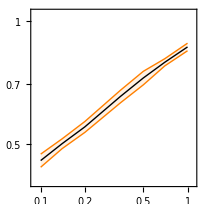

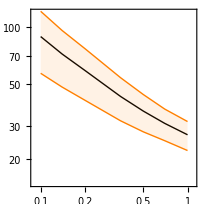

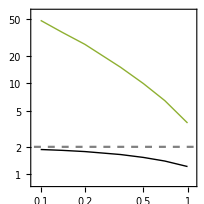

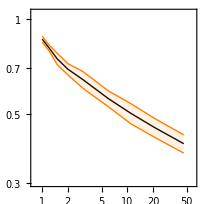

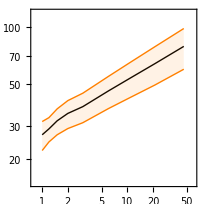

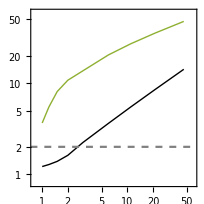

```mathematica
gammadevlistC = Table[
Psiklist[lstarlistC[[j]],ll0,ffb,clist[[j]],0,0]; 
gl = Transpose[Select[plist, #[[2]]>Max[Transpose[plist][[2]]]-1&]][[1]];
stdev = (Max[gl]-Max[Min[gl],gamma1[lstarlistC[[j]],ll0]])/2;
stdev,
{j,1, Length[clist]}];

p4a= Show[
ListLogLogPlot[{Table[{clist[[j]]/ll0,gammalstarlistC[[j]] }, {j,1,Length[clist]}],
Reverse[Table[{clist[[j]]/ll0, gammalstarlistC[[j]]+ gammadevlistC[[j]]}, {j,1,Length[clist]}]],
Reverse[Table[{clist[[j]]/ll0, gammalstarlistC[[j]]- gammadevlistC[[j]]}, {j,1,Length[clist]}]]},
Frame -> True,Joined -> True, PlotRange->{{0.09,1.1},{0.4,1.05}},AspectRatio -> 1,
 PlotStyle -> {{ Thick, Black}, {Thin, Orange},{Thin, Orange}},
(* FrameLabel->{"cost per unit code length, 2Nc_0", "coding density, γ"}*)
Filling-> {2->{3}}, FillingStyle -> Opacity[0.1]
]
]

ldevlistC = Table[
lf = Fit[Table[{l,flist2C[[j,l]]}, {l,Max[lstarlistC[[j]]-Ceiling[lstarlistC[[j]]/5], lmlistC[[j]]+1],lstarlistC[[j]]+Ceiling[lstarlistC[[j]]/5]}], {1,l,l^2},l];
stdev = (-Coefficient[lf, l^2])^(-1/2);
stdev,
{j,1, Length[clist]}];

p4b = Show[
ListLogLogPlot[Transpose[{clist/ll0, lstarlistC}],
Frame -> True, 
(*FrameLabel->{"cost per unit code length, 2Nc_0","code length, l"},*) 
(*LabelStyle->{{Automatic,ColorData[97,3]},{Automatic,Automatic}},*)
AspectRatio -> 1 ,
PlotRange-> (*{{0.8,60},{12,99}}*) {{0.09,1.1},{15,119}}, 
Joined -> True,PlotStyle -> {Thick, Black}],

ListLogLogPlot[
{Reverse[Table[{clist[[j]]/ll0, lstarlistC[[j]]+ ldevlistC[[j]]}, {j,1,Length[clist]}]],
Reverse[Table[{clist[[j]]/ll0, lstarlistC[[j]]- ldevlistC[[j]]}, {j,1,Length[clist]}]]},
Joined -> True,PlotStyle -> {{Thin, Orange},{Thin, Orange}}, 
Filling-> {2-> {1}}, FillingStyle -> Opacity[0.1]]]


p4c = Show[ListLogLogPlot[
Table[{clist[[j]]/ll0, 2 vplusstar[lstarlistC[[j]],ll0,ffb,clist[[j]],0,0]}, {j,1,Length[clist]}], 
PlotRange -> {{0.09,1.1},{0.8,59}}, Joined -> True,
Joined -> True,PlotStyle -> {Thick, Black},
Frame -> True,
(* FrameLabel->{{"ratchet rate, v_tot","adaptive width, A"} ,{"cost per unit sequence, c", Null}} *)
(* FrameLabel->{"driving rate, (1+κ)", "rate, v_tot,  width, A"} *) 
AspectRatio ->1],

ListLogLogPlot[Table[{clist[[j]]/ll0, lstarlistC[[j]](1 - gammalstarlistC[[j]])}, {j,1,Length[clist]}],
(* AspectRatio -> 1, *) 
Joined -> True,PlotStyle -> {Thick, ColorData[97,3]}],

LogLogPlot[2, {x,0.09,1.1}, PlotStyle -> {Gray,Dashed}]]

gammadevlist = Table[
Psiklist[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]; 
gl = Transpose[Select[plist, #[[2]]>Max[Transpose[plist][[2]]]-1&]][[1]];
stdev = (Max[gl]-Max[Min[gl],gamma1[lstarlist[[i]],ll0]])/2;
stdev,
{i,1, Length[kappalist]}];

p4d= Show[
ListLogLogPlot[Table[{1+kappalist[[i]],gammalstarlist[[i]] }, {i,1,Length[kappalist]}],
Frame -> True, PlotRange->{{0.8,60},{0.3,1.05}},AspectRatio -> 1,
Joined -> True, PlotStyle -> { Thick, Black}
(* FrameLabel->{"driving rate, (1+κ)", "coding density, γ"}*) ], 
ListLogLogPlot[
{Table[{1 + kappalist[[i]], gammalstarlist[[i]]+ gammadevlist[[i]]}, {i,1,Length[kappalist]}],
Table[{1 + kappalist[[i]], gammalstarlist[[i]]-gammadevlist[[i]]}, {i,1,Length[kappalist]}]},
Joined -> True,PlotStyle -> {{Thin, Orange},{Thin, Orange}}, 
Filling-> {1->{2}}, FillingStyle -> Opacity[0.1]]
]

ldevlist = Table[
lf = Fit[Table[{l,flist2[[i,l]]}, {l,Max[lstarlist[[i]]-Ceiling[lstarlist[[i]]/5], lmlist[[i]]+1],lstarlist[[i]]+Ceiling[lstarlist[[i]]/5]}], {1,l,l^2},l];
stdev = (-Coefficient[lf, l^2])^(-1/2);
stdev,
{i,1, Length[kappalist]}];

p4e = Show[
ListLogLogPlot[Transpose[{1 + kappalist, lstarlist}],
Frame -> True, 
(* FrameLabel->{"driving rate, (1+κ)","code length, l"},*) 
(*LabelStyle->{{Automatic,ColorData[97,3]},{Automatic,Automatic}},*)
AspectRatio -> 1 ,
PlotRange-> (*{{0.8,60},{12,99}}*) {{0.8,60},{15,119}}, 
Joined -> True,PlotStyle -> {Thick, Black}],

ListLogLogPlot[
{Table[{1 + kappalist[[i]], lstarlist[[i]]+ ldevlist[[i]]}, {i,1,Length[kappalist]}],
Table[{1 + kappalist[[i]], lstarlist[[i]]-ldevlist[[i]]}, {i,1,Length[kappalist]}]},
Joined -> True,PlotStyle -> {{Thin, Orange},{Thin, Orange}}, 
Filling-> {1->{2}}, FillingStyle -> Opacity[0.1]]]


p4f = Show[ListLogLogPlot[
Table[{1+kappalist[[i]], 2 vplusstar[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, {i,1,Length[kappalist]}], 
PlotRange -> {{0.8,60},{0.8,59}}, Joined -> True,
Joined -> True,PlotStyle -> {Thick, Black},
Frame -> True ,
(*FrameLabel->{{"ratchet rate, v_tot","adaptive width, A"} ,{"driving rate, (1+κ)", Null}} *)
(* FrameLabel->{"driving rate, (1+κ)", "rate, v_tot,  width, A"} *) 
AspectRatio ->1],

ListLogLogPlot[Table[{1 + kappalist[[i]], lstarlist[[i]](1 - gammalstarlist[[i]])}, {i,1,Length[kappalist]}],
(* AspectRatio -> 1, *) 
Joined -> True,PlotStyle -> {Thick, ColorData[97,3]}],

LogLogPlot[2, {x,0.5,60}, PlotStyle -> {Gray,Dashed}]]
```

```mathematica
(* Figure S4: Evolutionary paths with loss of function *) 

kltrajS[path_]:=Table[{path⟦t,2⟧,34-path⟦t,1⟧ path⟦t,2⟧},{t,1,Length[path]}] 

(* runs  for Fig. S1 *) 

evol2[20,ll0,ffb,ffc,0,45,0.1,10000];
Print[next]
Print[ nad]
Print[ ndel]
GraphicsGrid[{{
(* trait evolution *) 
Show[
MatrixPlot[Table[0, {k,1,35}, {l,1,100}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30},{1,10,20,30}},{{1,20,40,60,80,100}, {1,20,40,60,80,100}}}],
(* Contours *) 
ContourPlot[Fb[(45-k)/l,l,ll0,ffb] , {l,1,100} ,{k,1,35},Contours->25, ContourShading -> False, ContourStyle-> Lighter[Gray], AspectRatio-> 0.27],
(*Graphics[Table[{PointSize[Medium],Darker[Orange],Point[{lstarlist[[i]], 44-lstarlist[[i]] gammalstarlist[[i]]}]}, {i,{1,3,5,6,7,8,9}}]],*)
(* path *) 
Graphics[{ColorData[97,1],Line[kltrajS[path]]}],
Graphics[{ColorData[97,3],PointSize[Medium],
Table[Point[{admutlist[[i,2]], 34 - admutlist[[i,1]]admutlist[[i,2]]}],{i,1,Length[admutlist]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[Medium],
Table[Point[{negmutlist[[i,2]], 34 - negmutlist[[i,1]]negmutlist[[i,2]]}],{i,1,Length[negmutlist]}]}],
Graphics[{ColorData[97,4],PointSize[Medium],
Table[Point[{elist[[i,2]], 34 - elist[[i,1]]elist[[i,2]]}],{i,1,Length[elist]}]}]]},
{(* length evolution *)
Show[MatrixPlot[Table[0, {k,1,35}, {l,1,100}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30},{1,10,20,30}},{{1,20,40,60,80,100}, {1,20,40,60,80,100}}}],
(* Contours *) 
ContourPlot[F[(35-k)/l,l,ll0,ffb,ffc,0] , {l,1,100} ,{k,1,35},Contours->25, ContourShading -> False, ContourStyle-> Lighter[Gray], AspectRatio-> 0.27],
(* path *) 
Graphics[{ColorData[97,1],Line[kltrajS[path]]}],
Graphics[{ColorData[97,3],PointSize[Medium],
Table[Point[{adlist[[i,2]], 34 - adlist[[i,1]]adlist[[i,2]]}],{i,1,Length[adlist]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[Medium],
Table[Point[{neglist[[i,2]], 34 - neglist[[i,1]]neglist[[i,2]]}],{i,1,Length[neglist]}]}]]
}}];

1864
120
16
-Graphics-

(* save for Fig. S1: run from evol2[20,ll0,ffb,ffc,0,10,0.1,10000] *) 
pathS2a = path; 
admutlistS2a= admutlist;
negmutlistS2a = negmutlist;
elistS2a = elist;
adlistS2a=adlist;
neglistS2a= neglist;

evol2[60,ll0,ffb,ffc,0,45,0.1,2000];
Print[next]
Print[ nad]
Print[ ndel]
GraphicsGrid[{{
(* trait evolution *) 
Show[
MatrixPlot[Table[0, {k,1,35}, {l,1,100}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30},{1,10,20,30}},{{1,20,40,60,80,100}, {1,20,40,60,80,100}}}],
(* Contours *) 
ContourPlot[Fb[(45-k)/l,l,ll0,ffb] , {l,1,100} ,{k,1,35},Contours->25, ContourShading -> False, ContourStyle-> Lighter[Gray], AspectRatio-> 0.27],
Graphics[Table[{PointSize[Medium],Darker[Orange],Point[{lstarlist[[i]], 44-lstarlist[[i]] gammalstarlist[[i]]}]}, {i,{1,3,5,6,7,8,9}}]],
(* path *) 
Graphics[{ColorData[97,1],Line[kltrajS[path]]}],
Graphics[{ColorData[97,3],PointSize[Medium],
Table[Point[{admutlist[[i,2]], 34 - admutlist[[i,1]]admutlist[[i,2]]}],{i,1,Length[admutlist]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[Medium],
Table[Point[{negmutlist[[i,2]], 34 - negmutlist[[i,1]]negmutlist[[i,2]]}],{i,1,Length[negmutlist]}]}],
Graphics[{ColorData[97,4],PointSize[Medium],
Table[Point[{elist[[i,2]], 34 - elist[[i,1]]elist[[i,2]]}],{i,1,Length[elist]}]}]]},
{(* length evolution *)
Show[MatrixPlot[Table[0, {k,1,35}, {l,1,100}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30},{1,10,20,30}},{{1,20,40,60,80,100}, {1,20,40,60,80,100}}}],
(* Contours *) 
ContourPlot[F[(35-k)/l,l,ll0,ffb,ffc,0] , {l,1,100} ,{k,1,35},Contours->25, ContourShading -> False, ContourStyle-> Lighter[Gray], AspectRatio-> 0.27],
(* path *) 
Graphics[{ColorData[97,1],Line[kltrajS[path]]}],
Graphics[{ColorData[97,3],PointSize[Medium],
Table[Point[{adlist[[i,2]], 34 - adlist[[i,1]]adlist[[i,2]]}],{i,1,Length[adlist]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[Medium],
Table[Point[{neglist[[i,2]], 34 - neglist[[i,1]]neglist[[i,2]]}],{i,1,Length[neglist]}]}]]
}}];

(* save for Fig. S1: run from evol2[60,ll0,ffb,ffc,0,45,0.1,2000] *) 
pathS2b = path; 
admutlistS2b= admutlist;
negmutlistS2b = negmutlist;
elistS2b = elist;
adlistS2b=adlist;
neglistS2b= neglist;
```

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Max::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

9787

129

84

1864

120

16

-Graphics-

1704

291

5

```mathematica
figS4a = 
(* (A) trait dynamics *) 
Show[
MatrixPlot[Table[0, {k,1,35}, {l,1,100}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30},{1,10,20,30}},{{1,20,40,60,80,100}, None}}], 
(* Contours *) 
ContourPlot[F[(35-k)/l,l,ll0,ffb,ffc,0] , {l,1,100} ,{k,1,35},Contours->20, ContourShading -> False, ContourStyle-> Lighter[Gray], AspectRatio-> 0.27],
(* path at kappa = 10 *) 
Graphics[{ColorData[97,1],Line[kltrajS[pathS2a]]}],
Graphics[{ColorData[97,3],PointSize[0.007],
Table[Point[{admutlistS2a[[i,2]], 34 - admutlistS2a[[i,1]]admutlistS2a[[i,2]]}],{i,1,Length[admutlistS2a]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.007],
Table[Point[{negmutlistS2a[[i,2]], 34 - negmutlistS2a[[i,1]]negmutlistS2a[[i,2]]}],{i,1,Length[negmutlistS2a]}]}],
Graphics[{ColorData[97,4],PointSize[0.007],
Table[Point[{elistS2a[[i,2]], 34 - elistS2a[[i,1]]elistS2a[[i,2]]}],{i,1,Length[elistS2a]}]}],
(* path at kappa = 45 *) 
Graphics[{ColorData[97,1],Line[kltrajS[pathS2b]]}],
Graphics[{ColorData[97,3],PointSize[0.007],
Table[Point[{admutlistS2b[[i,2]], 34 - admutlistS2b[[i,1]]admutlistS2b[[i,2]]}],{i,1,Length[admutlistS2b]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.007],
Table[Point[{negmutlistS2b[[i,2]], 34 - negmutlistS2b[[i,1]]negmutlistS2b[[i,2]]}],{i,1,Length[negmutlistS2b]}]}],
Graphics[{ColorData[97,4],PointSize[0.007],
Table[Point[{elistS2b[[i,2]], 34 - elistS2b[[i,1]]elistS2b[[i,2]]}],{i,1,Length[elistS2b]}]}]
(* FrameLabel->{"code length, StyleBox[\"l\",FontSlant->\"Italic\"]","number of matches, StyleBox[\"k\",FontSlant->\"Italic\"]"}*)]

(* (B) length dynamics *) 
figS4b = Show[
MatrixPlot[Table[0, {k,1,35}, {l,1,100}],AspectRatio-> 0.27,
FrameTicks->{{{1,10,20,30},{1,10,20,30}},{{1,20,40,60,80,100}, None}}], 
(* Contours *) 
ContourPlot[F[(35-k)/l,l,ll0,ffb,ffc,0] , {l,1,100} ,{k,1,35},Contours->20, ContourShading -> False, ContourStyle-> Lighter[Gray]],
(* path at kappa = 10 *) 
Graphics[{ColorData[97,1],Line[kltrajS[pathS2a]]}],
Graphics[{ColorData[97,3],PointSize[0.007],
Table[Point[{adlistS2a[[i,2]], 34 - adlistS2a[[i,1]]adlistS2a[[i,2]]}],{i,1,Length[adlistS2a]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.007],
Table[Point[{neglistS2a[[i,2]], 34 - neglistS2a[[i,1]]neglistS2a[[i,2]]}],{i,1,Length[neglistS2a]}]}],
(* path at kappa = 45 *) 
Graphics[{ColorData[97,1],Line[kltrajS[pathS2b]]}], 
Graphics[{ColorData[97,3],PointSize[0.007],
Table[Point[{adlistS2b[[i,2]], 34 - adlistS2b[[i,1]]adlistS2b[[i,2]]}],{i,1,Length[adlistS2b]}]}],
Graphics[{Darker[ColorData[97,4]],PointSize[0.007],
Table[Point[{neglistS2b[[i,2]], 34 - neglistS2b[[i,1]] neglistS2b[[i,2]]}],{i,1,Length[neglistS2b]}]}]
(* FrameLabel->{"code length, StyleBox[\"l\",FontSlant->\"Italic\"]","number of matches, StyleBox[\"k\",FontSlant->\"Italic\"]"}*)]
```

-Graphics-

-Graphics-

General::munfl: Exp[-809.679] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-862.438] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-746.698] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

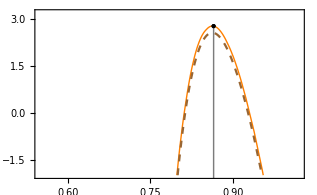

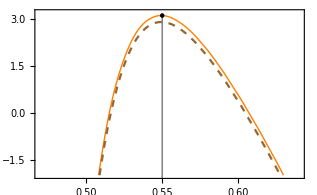

General::munfl: Exp[-1120.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2070.91] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3548.77] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

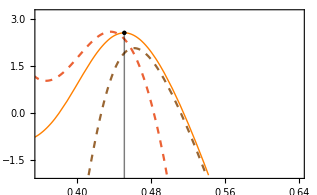

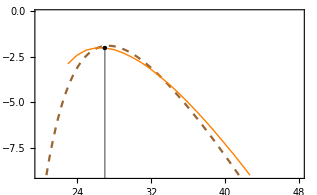

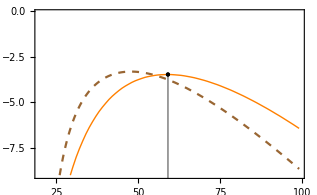

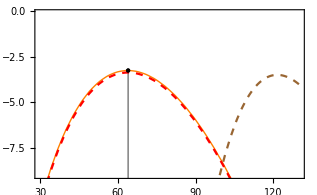

```mathematica
(* Figure S1: Approximate evolutionary potentials *)

fQGlognormlist= Table[
Log[Sum[Exp[(ffb ll0/2)(pb[gammastarlist2[[i,l]],l,ll0]-1)-ffc l/(ll0)],{l,lmlist[[i]]+1,150}]
], {i,1,Length[kappalist]}];

fQGlognormlistC= Table[
Log[Sum[Exp[(ffb ll0/2)(pb[gammastarlist2C[[j,l]],l,ll0]-1)-clist[[j]]l/(ll0)],{l,lmlistC[[j]]+1,150}]
], {j,1,Length[clist]}];

figS1a = Show[Table[Plot[{
Psik[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]] - Psiklognormlist[[i]],

PsikQ[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]-PsikQ[Min[1.5 gammalstarlist[[i]],1],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]+Psik[Min[1.5 gammalstarlist[[i]],1],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]] - Psiklognormlist[[i]]-0.2

(*PsikSC[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]-PsikSC[gammalstarlist[[i]],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]+Psik[gammalstarlist[[i]],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]- Psiklognormlist[[i]] -0.2*)},

{gamma,0.25,Min[1.5 gammalstarlist[[i]],1]}, PlotStyle -> {{Thick,Orange}, {Dashed,Brown}, {Dashed, ColorData[97,4]}}, 
PlotRange ->{{0.55,1.02},{-2,3.2}},
Frame -> True, Axes-> None 
(* FrameLabel->{"coding density, γ", "evolutionary potential, Ψ"}*)], 
{i,{1}}],
Table[ListPlot[{{gammalstarlist[[i]],Psik[gammalstarlist[[i]],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]- Psiklognormlist[[i]]}}, PlotStyle-> {Black, PointSize[Medium]},Filling ->-5],{i,{1}}]] 

figS1b = Show[Table[Plot[{
Psik[gamma,lstarlistC[[j]],ll0,ffb,0,0,0] - PsiklognormlistC[[j]],

PsikQ[gamma,lstarlistC[[j]],ll0,ffb,0,0,0]-
PsikQ[Min[1.5 gammalstarlistC[[j]],1],lstarlistC[[j]],ll0,ffb,0,0,0]+Psik[Min[1.5 gammalstarlistC[[j]],1],lstarlistC[[j]],ll0,ffb,0,0,0] - PsiklognormlistC[[j]]-0.2},

{gamma,0.25,Min[1.5 gammalstarlistC[[j]],1]}, PlotStyle -> {{Thick,Orange}, {Dashed,Brown}, {Dashed, ColorData[97,4]}}, 
PlotRange ->{{0.47,0.64},{-2,3.2}},
Frame -> True, Axes-> None
(* FrameLabel->{"coding density, γ", "evolutionary potential, Ψ"}*)], 
{j,{5}}],
Table[ListPlot[{{gammalstarlistC[[j]],Psik[gammalstarlistC[[j]],lstarlistC[[j]],ll0,ffb,0,0,0]- PsiklognormlistC[[j]]}}, PlotStyle-> {Black, PointSize[Medium]},Filling ->-5],{j,{5}}]] 

 figS1c = Show[Table[Plot[{
Psik[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]] - Psiklognormlist[[i]],

PsikQ[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]-PsikQ[Min[1.5 gammalstarlist[[i]],1],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]+Psik[Min[1.5 gammalstarlist[[i]],1],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]] - Psiklognormlist[[i]]-0.2,

PsikSC[gamma,lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]-PsikSC[gammalstarlist[[i]],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]+Psik[gammalstarlist[[i]],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]- Psiklognormlist[[i]] -0.2},

{gamma,0.25,Min[1.5 gammalstarlist[[i]],1]}, PlotStyle -> {{Thick,Orange}, {Dashed,Brown}, {Dashed, ColorData[97,4]}}, 
PlotRange ->{{0.36,0.64},{-2,3.2}},
Frame -> True, Axes->None 
(* FrameLabel->{"coding density, γ", "evolutionary potential, Ψ"} *) 
(*FrameTicks->{{Automatic,None},{{0.4,0.5,0.6},None}}*)],
{i,{8}}],
Table[ListPlot[{{gammalstarlist[[i]],Psik[gammalstarlist[[i]],lstarlist[[i]],ll0,ffb,0,0,kappalist[[i]]]- Psiklognormlist[[i]]}}, PlotStyle-> {Black, PointSize[Medium]},Filling ->-5],{i,{8}}]] 

figS1d = Show[Table[ft=Fit[Table[{l,(ffb ll0/2)(pb[gammastarlist2[[i,l]],l,ll0]-1)-ffc l/(ll0)}, {l,lmlist[[i]]+1,150}],
{1,1/l,1/l^2,1/l^3, 1/l^4,l},l];
Plot[ft -fQGlognormlist[[i]], {l,15,99},
Frame -> True, 
(* FrameLabel->{"code length, l", "evolutionary potential, Ψ"} , *) 
PlotStyle -> {Dashed, Brown}, PlotRange ->{{20,48},{-9,-0.1}}],{i,{1}}],

Table[ListPlot[Table[{l,flist2[[i,l]]- flognormlist[[i]]}, {l,1,99}], 
PlotStyle -> {Thick, Orange}, Joined -> True, PlotRange ->{{20,99},{-9,-0.1}},
Frame -> True
(* FrameLabel->{"code length, l", "evolutionary potential, Ψ"}*) ], 
{i,{1}}],

Table[ListPlot[{{lstarlist[[i]],flist2[[i,lstarlist[[i]]]]- flognormlist[[i]]}}, PlotStyle-> {Black, PointSize[Medium]},Filling ->-20],
{i,{1}}]]

figS1e = Show[Table[ft=Fit[Table[{l,(ffb ll0/2)(pb[gammastarlist2C[[j,l]],l,ll0]-1)-clist[[j]] l/(ll0)}, {l,lmlistC[[j]]+1,150}],
{1,1/l,1/l^2,1/l^3, 1/l^4,l},l];
Plot[ft -fQGlognormlistC[[j]], {l,15,99},
Frame -> True, 
(* FrameLabel->{"code length, l", "evolutionary potential, Ψ"}, *) 
PlotStyle -> {Dashed, Brown}, PlotRange ->{{20,99},{-9,-0.1}}],
{j,{5}}],

Table[ListPlot[Table[{l,flist2C[[j,l]]- flognormlistC[[j]]}, {l,1,99}], 
PlotStyle -> {Thick, Orange}, Joined -> True, PlotRange ->{{20,99},{-9,-0.1}},
Frame -> True
(* FrameLabel->{"code length, l", "evolutionary potential, Ψ"}*) ], 
{j,{5}}],

Table[ListPlot[{{lstarlistC[[j]],flist2C[[j,lstarlistC[[j]]]]- flognormlistC[[j]]}}, PlotStyle-> {Black, PointSize[Medium]},Filling ->-20],
{j,{5}}]]

figS1f = Show[Table[ft=Fit[Table[{l,(ffb ll0/2)(pb[gammastarlist2[[i,l]],l,ll0]-1)-ffc l/(ll0)}, {l,lmlist[[i]]+1,150}],
{1,1/l,1/l^2,1/l^3, 1/l^4,l},l];
Plot[ft -fQGlognormlist[[i]], {l,30,130},
Frame -> True, 
(* FrameLabel->{"code length, l", "evolutionary potential, Ψ"}*) 
PlotStyle -> {Dashed, Brown}, PlotRange ->{{30,130},{-9,-0.1}}],{i,{8}}],

Table[ListPlot[Table[{l,flist2[[i,l]]- flognormlist[[i]]}, {l,1,130}], 
PlotStyle -> {Thick, Orange}, Joined -> True], 
{i,{8}}],
Table[ListPlot[{{lstarlist[[i]],flist2[[i,lstarlist[[i]]]]- flognormlist[[i]]}}, 
PlotStyle-> {Black, PointSize[Medium]},Filling ->-20],
{i,{8}}],

Table[ListPlot[Table[{l,flistSC2[[i,l]]- flognormlist[[i]]-0.11}, {l,1,130}], 
PlotStyle -> {Dashed, Red}, Joined -> True], 
{i,{8}}]]
```

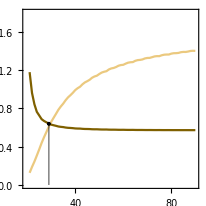

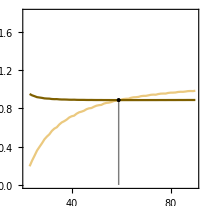

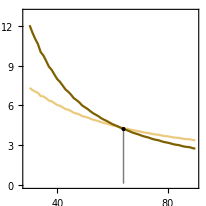

```mathematica
(* Figure S2: Ratchet dynamics
(a) Rates v_+(\ell, \kappa) and v_-(\ell, \kappa), 
(b) ratchet selection coefficients seffplus, seffminus, 
(c) total ratchet rate, v_tot (\ell, \kappa), and net elongation rate, v_e (\ell, \kappa. *)

figS2a= 
Show[Table[
ListPlot[{
(*Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]/g[seff[l,ll0,ffb,ffc,0,kappalist[[i]]]]}, {l,lmlist[[i]]+1,120}],*)
Table[{l, v = vminusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}],
Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}]},
PlotStyle ->{RGBColor[235/255,201/255,127/255], RGBColor[127/255,96/255,0/255]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "rates, v_+, v_-"}, *) 
PlotRange -> {0.,1.8}],
{i,{2}}], 

ListPlot[Table[{lstarlist[[i]],vplusstar[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, {i,{2}}],PlotStyle -> Black, Filling -> 0]]

figS2b= 
Show[Table[
ListPlot[{
(*Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]/g[seff[l,ll0,ffb,ffc,0,kappalist[[i]]]]}, {l,lmlist[[i]]+1,120}],*)
Table[{l, v = vminusstar[l,ll0,ffb,clist[[j]],0,0]}, {l,lmlistC[[j]]+1,90}],
Table[{l, v = vplusstar[l,ll0,ffb,clist[[j]],0,0]}, {l,lmlistC[[j]]+1,90}]},
PlotStyle ->{RGBColor[235/255,201/255,127/255], RGBColor[127/255,96/255,0/255]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "rates, v_+, v_-"},*) 
PlotRange -> {0.,1.8}],
{j,{5}}], 

ListPlot[Table[{lstarlistC[[j]],vplusstar[lstarlistC[[j]],ll0,ffb,clist[[j]],0,0]}, {j,{5}}],PlotStyle -> Black, Filling -> 0]]

figS2c= 
Show[Table[
ListPlot[{
(*Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]/g[seff[l,ll0,ffb,ffc,0,kappalist[[i]]]]}, {l,lmlist[[i]]+1,120}],*)
Table[{l, v = vminusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}],
Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}]},
PlotStyle ->{RGBColor[235/255,201/255,127/255], RGBColor[127/255,96/255,0/255]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "rates, v_+, v_-"},*) 
PlotRange -> {0.,13}],
{i,{8}}], 

ListPlot[Table[{lstarlist[[i]],vplusstar[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, 
{i,{8}}],PlotStyle -> Black, Filling -> 0.1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

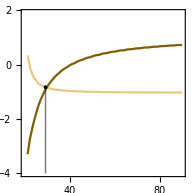

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

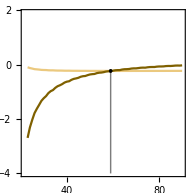

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

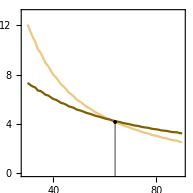

```mathematica
figS2d= 
Show[
Table[
ListPlot[{
(*Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]/g[seff[l,ll0,ffb,ffc,0,kappalist[[i]]]]}, {l,lmlist[[i]]+1,120}],*)
Table[{l, v = seffplus[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}],
Table[{l, v = seffminus[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}]},
PlotStyle ->{RGBColor[235/255,201/255,127/255], RGBColor[127/255,96/255,0/255]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "selection, s_+, s_-"},*) 
PlotRange -> {-4,1.9}],
{i,{2}}], 

ListPlot[Table[{lstarlist[[i]],seffplus[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, {i,{2}}],PlotStyle -> Black, Filling -> -4]]

figS2e= 
Show[
Table[
ListPlot[{
(*Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]/g[seff[l,ll0,ffb,ffc,0,kappalist[[i]]]]}, {l,lmlist[[i]]+1,120}],*)
Table[{l, v = seffplus[l,ll0,ffb,clist[[j]],0,0]}, {l,lmlistC[[j]]+1,90}],
Table[{l, v = seffminus[l,ll0,ffb,clist[[j]],0,0]}, {l,lmlistC[[j]]+1,90}]},
PlotStyle ->{RGBColor[235/255,201/255,127/255], RGBColor[127/255,96/255,0/255]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "selection, s_+, s_-"},*) 
PlotRange -> {-4,1.9}],
{j,{5}}], 

ListPlot[Table[{lstarlistC[[j]],seffplus[lstarlistC[[j]],ll0,ffb,clist[[j]],0,0]}, {j,{5}}],PlotStyle -> Black, Filling -> -4]]

figS2f= 
Show[
Table[
ListPlot[{
(*Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]/g[seff[l,ll0,ffb,ffc,0,kappalist[[i]]]]}, {l,lmlist[[i]]+1,120}],*)
Table[{l, v = seffplus[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}],
Table[{l, v = seffminus[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}]},
PlotStyle ->{RGBColor[235/255,201/255,127/255], RGBColor[127/255,96/255,0/255]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "selection, s_+, s_-"},*) 
PlotRange -> {0,13}],
{i,{8}}], 

ListPlot[Table[{lstarlist[[i]],seffplus[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, {i,{8}}],PlotStyle -> Black, Filling -> -3]]
```

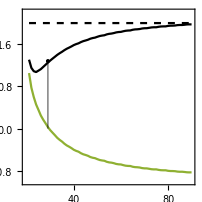

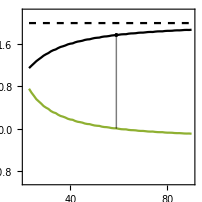

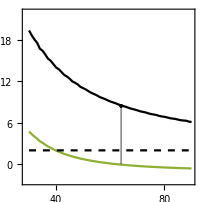

```mathematica
figS2g= Show[Table[
ListPlot[{
Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]] + vminusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}],
Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]] - vminusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}]},
PlotStyle ->{Black, ColorData[97,3]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "rates, v_tot, v_e"},*) 
PlotRange -> {-1,2.2}],
{i,{2}}], 
ListPlot[Table[{lstarlist[[i]],2 vplusstar[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, {i,{2}}],PlotStyle -> Black, Filling -> 0.], 
Plot[2, {l,lmlist[[2]]+1,90}, PlotStyle -> {Black, Dashed}]
]

figS2h= Show[Table[
ListPlot[{
Table[{l, v = vplusstar[l,ll0,ffb,clist[[j]],0,0] + vminusstar[l,ll0,ffb,clist[[j]],0,0]}, {l,lmlistC[[j]]+1,90}],
Table[{l, v = vplusstar[l,ll0,ffb,clist[[j]],0,0] - vminusstar[l,ll0,ffb,clist[[j]],0,0]}, {l,lmlistC[[j]]+1,90}]
},
PlotStyle ->{Black, ColorData[97,3]},
Joined -> True,Frame -> True, AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "rates, v_tot, v_e"},*) 
PlotRange -> {-1,2.2}],
{j,{5}}], 
ListPlot[Table[{lstarlistC[[j]],2 vplusstar[lstarlistC[[j]],ll0,ffb,clist[[j]],0,0]}, {j,{5}}],PlotStyle -> Black, Filling -> 0.], 
Plot[2, {l,lmlistC[[5]]+1,90}, PlotStyle -> {Black, Dashed}]
]

figS2i= Show[Table[
ListPlot[{
Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]] + vminusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}],
Table[{l, v = vplusstar[l,ll0,ffb,ffc,0,kappalist[[i]]] - vminusstar[l,ll0,ffb,ffc,0,kappalist[[i]]]}, {l,lmlist[[i]]+1,90}]},
PlotStyle ->{Black, ColorData[97,3]},
Joined -> True,Frame -> True, Axes -> True,AspectRatio -> 1, 
(* FrameLabel->{"code length, l", "rates, v_tot, v_e"},*) 
PlotRange -> {-2.5,22}],
{i,{8}}], 
ListPlot[Table[{lstarlist[[i]],2 vplusstar[lstarlist[[i]],ll0,ffb,ffc,0,kappalist[[i]]]}, {i,{8}}],PlotStyle -> Black, Filling -> 0.], 
Plot[2, {l,lmlist[[8]]+1,90}, PlotStyle -> {Black, Dashed}]
]
```

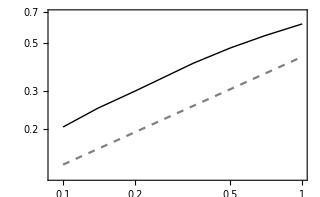

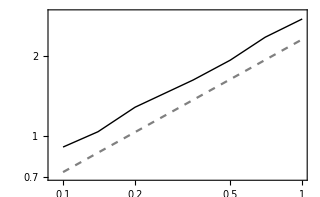

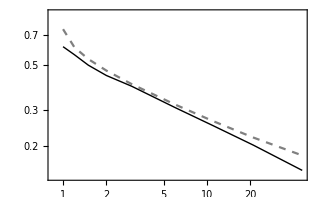

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

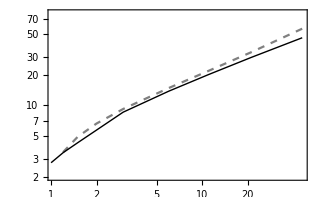

```mathematica
(* Fig. S3: Comparison of ML points from full solution and approximate closure *) 
cpp=1-Exp[-gap/ll0 (1-gamma0)];
cmp=1-Exp[-gap/ll0 *gamma0];
cnu=2Sinh[gap/ll0/2];
(* weak driving, coding density *) 
figS3a = 
Show[ListLogLogPlot[Transpose[{clist / ll0, gammalstarlistC -gamma0}], 
Joined -> True, Frame -> True, PlotStyle -> {Thick, Black}, PlotRange ->{0.12,0.69}(* FrameLabel-> {"cost per unit code length, 2Nc_0", "ML coding density, γ^*- γ_0 "}*) ],  
LogLogPlot[(c gamma0 (1 - gamma0))^(1/2), {c,0.1,1}, PlotStyle -> {Dashed, Gray}]]

(* weak driving, selection on recognition *) 
figS3b = Show[ListLogLogPlot[Table[{clist[[i]] / ll0, -Fb[gammalstarlistC[[i]]-1/(2lstarlistC[[i]]), lstarlistC[[i]],ll0,ffb] + Fb[gammalstarlistC[[i]]+1/(2lstarlistC[[i]]), lstarlistC[[i]],ll0,ffb]},{i,1,Length[clist]}], 
Joined -> True, Frame -> True, PlotStyle -> {Thick, Black},PlotRange ->{0.7,2.9}(* FrameLabel-> {"cost per unit code length, 2Nc_0", "ML selection, 2Ns_γ^*"} *) ],
LogLogPlot[(c /(gamma0 (1 - gamma0)))^(1/2), {c,0.1,1}, PlotStyle -> {Dashed, Gray}]]

(* strong driving, coding density *) 
figS3c = Show[ListLogLogPlot[ Table[{1+ kappalist[[i]], x -g0/.Solve[(x - g0) / (g0 (1-x))*kappa == (1-x+g0) / (g0 * cpp - (1-x)*cmp)*cnu, x] [[1]]/. ep0 -> gap /ll0 /. g0->gamma0 /. l0->ll0 /. lmbda ->1 /. kappa-> kappalist[[i]]},{i,1,Length[kappalist]}], 
PlotRange -> {0.14, 0.9},Joined -> True, PlotStyle -> {Dashed, Gray}, Frame -> True, 
(* FrameLabel-> {"driving rate, (1+κ)", "ML coding density, γ^*- γ_0"},*) 
AspectRatio -> 1/GoldenRatio], 
ListLogLogPlot[ 
Table[{1+ kappalist[[i]], gammalstarlist[[i]] - gamma0},{i,1,Length[kappalist]}], 
Joined -> True, PlotStyle -> {Thick, Black}, PlotRange -> {0.1, 0.8}]
]

(* strong driving, selection on recognition *) 
figS3d = Show[
ListLogLogPlot[ Table[{1+ kappalist[[i]], (x-g0)/(g0(1-x)) *kappa
/.Solve[(x - g0) / (g0 (1-x))*kappa == (1-x+g0) / (g0 * cpp - (1-x)*cmp)*cnu, x] [[1]]
/. ep0 -> gap /ll0 /. g0->gamma0 /. l0->ll0 /. lmbda ->1 /. kappa-> kappalist[[i]]},{i,1,Length[kappalist]}], 
Joined -> True, PlotStyle -> {Dashed, Gray}, Frame -> True, 
(* FrameLabel-> {"driving rate, (1+κ)", "ML selection, 2Ns_γ^*"},*) 
AspectRatio -> 1/GoldenRatio, PlotRange->{2,80}],
ListLogLogPlot[ 
Table[{1+ kappalist[[i]], (F[gammalstarlist[[i]]+1/(2 lstarlist[[i]]),lstarlist[[i]],ll0,ffb,ffc,0]-F[gammalstarlist[[i]]-1/(2 lstarlist[[i]]),lstarlist[[i]],ll0,ffb,ffc,0])},{i,1,Length[kappalist]}], 
Joined -> True, PlotStyle -> {Thick, Black}]
]
```